# Test HHGraphicLabel (and AbsoluteOptions)

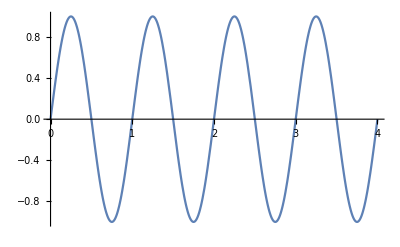

```mathematica
testGr=Plot[Sin[x*2 Pi], {x, 0, 4}]
```

## Playing Around

```mathematica
AbsoluteOptions[testGr]
```

{AlignmentPoint→Center,AspectRatio→0.618034,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0.,0.},AxesStyle→{{GrayLevel[0.],AbsoluteThickness[0.25]},{GrayLevel[0.],AbsoluteThickness[0.25]}},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FormatType→TraditionalForm,Frame→{False,False,False,False},FrameLabel→{{None,None},{None,None}},FrameStyle→{{},{},{},{}},FrameTicks→{None,None,None,None},FrameTicksStyle→{},GridLines→{{},{}},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→{DefaultBoundaryStyle→Automatic,DefaultMeshStyle→AbsolutePointSize[6.],ScalingFunctions→None,CoordinatesToolOptions→{DisplayFunction→({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}},PlotLabel→None,PlotRange→{{0.,4.},{-0.999997,0.999998}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→{{{0.,0.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{0.5,0.5,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{1.,1.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{1.5,1.5,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{2.,2.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{2.5,2.5,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{3.,3.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{3.5,3.5,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{4.,4.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{0.1,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.2,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.3,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.4,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.6,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.7,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.8,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.9,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.1,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.2,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.3,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.4,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.6,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.7,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.8,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{1.9,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.1,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.2,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.3,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.4,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.6,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.7,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.8,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{2.9,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.1,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.2,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.3,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.4,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.6,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.7,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.8,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{3.9,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}}},{{-1.,-1.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{-0.75,-0.75,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{-0.5,-0.5,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{-0.25,-0.25,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{0.,0.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{0.25,0.25,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{0.5,0.5,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{0.75,0.75,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{1.,1.,{0.00625,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{-0.95,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.9,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.85,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.8,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.7,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.65,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.6,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.55,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.45,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.4,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.35,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.3,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.2,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.15,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.1,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{-0.05,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.05,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.1,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.15,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.2,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.3,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.35,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.4,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.45,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.55,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.6,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.65,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.7,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.8,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.85,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.9,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}},{0.95,,{0.00375,0.},{GrayLevel[0.],AbsoluteThickness[0.125]}}}},TicksStyle→{}}

```mathematica
AbsoluteOptions[testGr, PlotRange]
```

{PlotRange→{{0.,4.},{-0.999997,0.999998}}}

```mathematica
absPlotRange=AbsoluteOptions[testGr, PlotRange][[1, 2]]
```

{{0.,4.},{-0.999997,0.999998}}

```mathematica
AbsoluteOptions[Graphics[], PlotRange]
```

{PlotRange→{{0.,1.},{0.,1.}}}

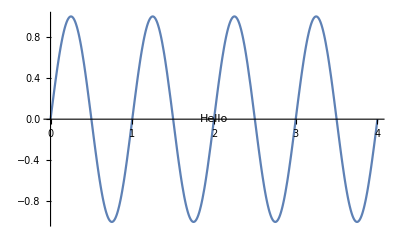

```mathematica
Show[testGr,
Graphics[Text["Hello",{2,0}]]
]
```

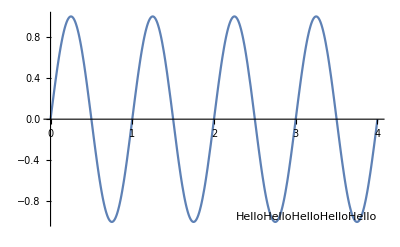

```mathematica
Show[testGr,
Graphics[
Text["HelloHelloHelloHelloHello",
{absPlotRange[[1,2]],absPlotRange[[2,1]]}, {1,-1} 
]]
]
```

```mathematica
Show[testGr,
Graphics[
Text["HelloHelloHelloHelloHello",
{absPlotRange[[1,2]],absPlotRange[[2,1]]}, {Right,Bottom} 
]]
]
```

-Graphics-

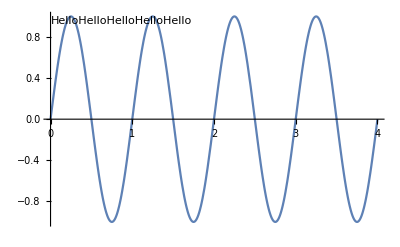

```mathematica
Show[testGr,
Graphics[
Text["HelloHelloHelloHelloHello",
{absPlotRange[[1,1]],absPlotRange[[2,2]]}, {Left,Top} 
]]
]
```

```mathematica
Left == Left
```

True

```mathematica
Top === Top
```

True

## Test Function

```mathematica
<<HokahokaW`Graphics`
```

```mathematica
Options[HHLabelGraphics]
```

{HHOptLabelStyleSpecifications→Tiny}

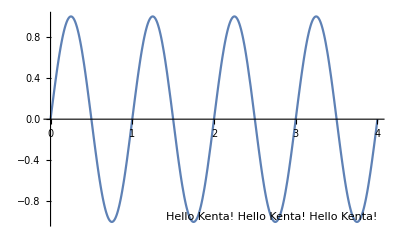

```mathematica
HHLabelGraphics[ testGr, "Hello Kenta! Hello Kenta! Hello Kenta!"]
```

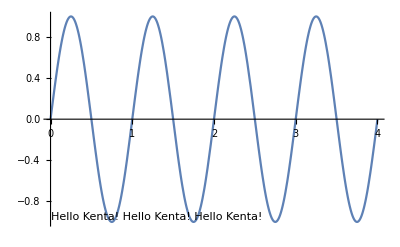

```mathematica
HHLabelGraphics[ testGr, "Hello Kenta! Hello Kenta! Hello Kenta!", {Left, Bottom}]
```

```mathematica
HHLabelGraphics[ testGr, "Hello Kenta! Hello Kenta! Hello Kenta!", {Left}]
```

-Graphics-

```mathematica
HHLabelGraphics[ testGr, "Hello Kenta! Hello Kenta! Hello Kenta!", {}]
```

-Graphics-